# 随机三角形网格

```mathematica
width=500;
height=500;
step=80;

dots=Table[{i+RandomReal[{-0.4,0.4}]step-If[EvenQ@(j/step),step/2,0],
j+RandomReal[{-0.4,0.4}]step},{i,0,width,step},{j,0,height,step}]
```

{{{-66.3588,-15.6695},{31.523,69.8374},{-20.7861,189.012},{-14.9413,223.805},{-55.733,327.828},{27.1656,372.368},{-41.9368,493.841}},{{46.7079,-6.49879},{69.5475,99.8301},{8.97931,153.095},{109.882,248.757},{48.2925,312.635},{76.1335,372.814},{31.2281,475.161}},{{104.262,4.98348},{150.64,74.1817},{98.4893,174.579},{136.807,221.972},{106.871,298.976},{180.651,374.602},{117.789,456.518}},{{227.906,-6.85486},{263.319,71.7068},{225.343,132.193},{248.905,226.87},{174.963,293.743},{222.664,389.954},{213.547,510.26}},{{268.854,25.2391},{335.476,83.525},{298.83,163.806},{331.802,235.705},{273.59,314.094},{350.072,396.725},{284.393,458.428}},{{331.335,18.7164},{409.57,106.352},{385.675,185.016},{399.082,247.697},{346.326,292.369},{416.38,374.056},{349.02,465.319}},{{413.842,-2.27021},{499.362,51.6332},{456.406,132.31},{497.634,260.695},{462.378,303.79},{480.443,378.587},{429.539,458.974}}}

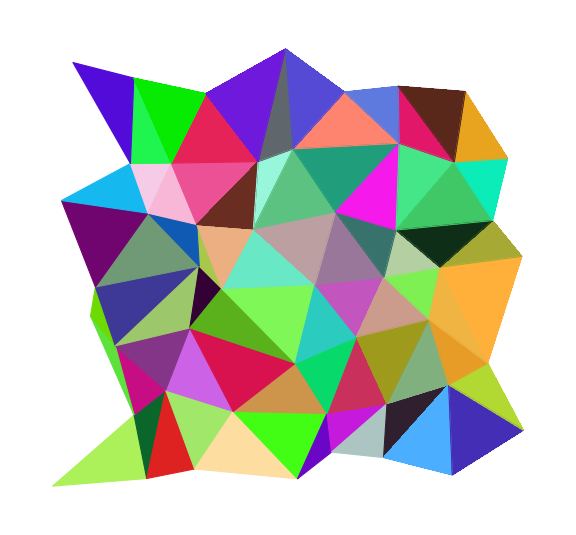

```mathematica
(*dots=Table[{i-If[EvenQ@(j/step),step/2,0],j},{i,0,width,step},{j,0,height,step}];*)

triangles={};

For[i=1,i<Length[dots],i++,
For[j=1,j<Length[dots[[i]]],j++,
If[EvenQ@j,
AppendTo[triangles,{dots[[i,j]],dots[[i+1,j]],dots[[i+1,j+1]]}];
AppendTo[triangles,{dots[[i,j]],dots[[i,j+1]],dots[[i+1,j+1]]}],
AppendTo[triangles,{dots[[i,j]],dots[[i,j+1]],dots[[i+1,j]]}];
AppendTo[triangles,{dots[[i,j+1]],dots[[i+1,j]],dots[[i+1,j+1]]}]
]
]]

Graphics[{JoinForm["Bevel"],EdgeForm[Thick],RandomColor[],Triangle[#]}&/@triangles,
ImageSize->Large]
```

## 最后看看用Javascript实现的效果